```mathematica
(*Directory of raw data*)
dir="C:/Documents/ResearchNotes/O(3)SurfaceTransition/SurfaceJQ3-draft/RawData/";
(*Directory of output figures*)
figdir="C:/Documents/ResearchNotes/O(3)SurfaceTransition/SurfaceJQ3-draft/figures/";
```

### Description of data files

#### Raw data from quantum Monte Carlo

File contents: L, Q, QMC mean value, QMC standard error

Rv.txt: Binder ratio of boundary VBS order parameter, denoted by R_v(Q,L) in the manuscript.

Cp.txt: Boundary half-length spin correlation function, denoted by C_∥(L/2) in the manuscript.

Sm.txt: static AF structure factor, denoted by S(L) in the manuscript.

Mv2.txt: static VBS structure factor, denoted by S_v(L) in the manuscript.

Mv.txt: VBS order parameter, denoted by v in the manuscript.

#### Generated ensemble of physical quantities with the resampling procedure

qSamples.txt: Generated Q_c values with the resampling procedure

ysSamples.txt: Generated y_s values with the resampling procedure

DsSamples.txt: Generated Δ_s values estimated from C_∥(L/2) with the resampling procedure

DsSamples2.txt: Generated Δ_s values estimated from S(L) with the resampling procedure

DvSamples.txt: Generated Δ_v values estimated from S_v(L) with the resampling procedure

DvSamples2.txt: Generated Δ_v values estimated from v with the resampling procedure

### Fig. 1: Model

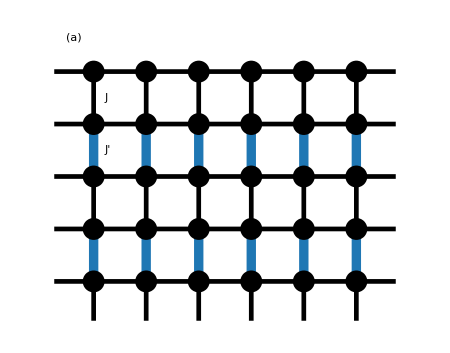

```mathematica
fig1a=Show[
Graphics[{
CapForm["Round"],Thickness[0.0075],Black,Table[Line[{{-0.75,i},{5.75,i}}],{i,1,4}],Table[Line[{{i,0.25},{i,5}}],{i,0,5}],
{Thickness[0.0075],Black,Line[{{-0.75,5},{5.75,5}}]},
{Thickness[0.015],blue,Table[Line[{{j,i},{j,i+1}}],{j,0,5},{i,1,3,2}]},
PointSize[0.035],Table[Point[{i,j}],{i,0,5},{j,1,5}],
FontSize->30,FontFamily->"Cambria",
Text["J",{0.2,4.5},{-1,0}],Text["J'",{0.2,3.5},{-1,0}],
Text["(a)",{-0.375,5.75},{0,1}]
}],
PlotRange->{{-1,6},{0.25,5.75}},ImageSize->{450,Automatic}]
```

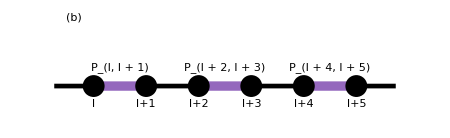

```mathematica
fig1b=Show[
Graphics[{
{CapForm["Round"],Thickness[0.0075],Black,Line[{{-0.75,0},{5.75,0}}]},
{Thickness[0.015],purple,Table[Line[{{j,0},{j+1,0}}],{j,0,4,2}]},
PointSize[0.035],Table[Point[{i,0}],{i,0,5}],
FontSize->30,FontFamily->"Cambria",
Text["P_(l, l + 1)",{0.5,0.25},{0,-1}],Text["P_(l + 2, l + 3)",{2.5,0.25},{0,-1}],Text["P_(l + 4, l + 5)",{4.5,0.25},{0,-1}],
Text["l",{0,-0.25},{0,1}],
Text["l+1",{1,-0.25},{0,1}],
Text["l+2",{2,-0.25},{0,1}],
Text["l+3",{3,-0.25},{0,1}],
Text["l+4",{4,-0.25},{0,1}],
Text["l+5",{5,-0.25},{0,1}],
Text["(b)",{-0.375,1.4},{0,1}]
}],
PlotRange->{{-1,6},{-0.75,1.4}},ImageSize->{450,Automatic}]
```

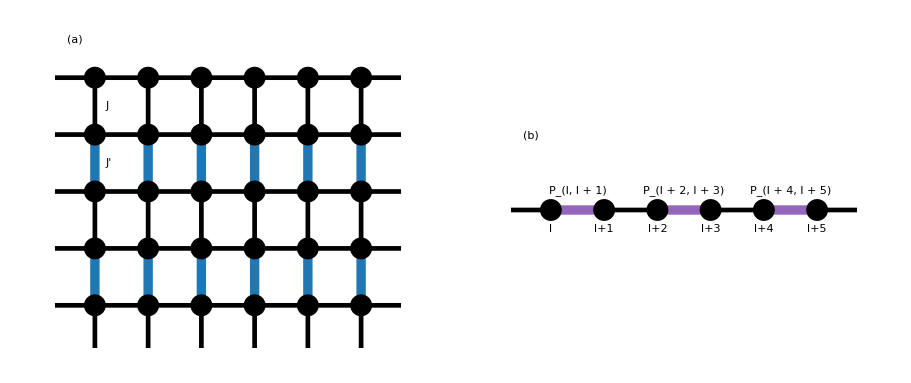

```mathematica
fig1=GraphicsRow[{fig1a,fig1b},Spacings->0]
Export[figdir<>"model.pdf",fig1,"PDF"];
```

### Fig. 2: Boundary transition

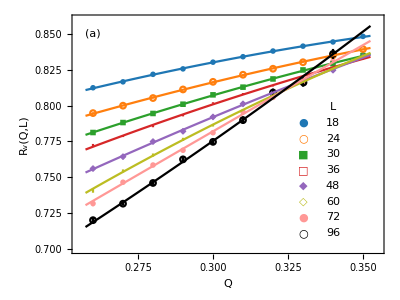

```mathematica
markers={disk,circle,square,rect,diam,diame,disk,circle};
markerstxt={"●","○","■","□","◆","◇","●","○"};
colors={blue,orange,green,red,purple,yellow,pink,Black};
qdlist=ReadList[dir<>"Rv.txt",Number];
qdlist=Partition[qdlist,{4}];
lenlist={18,24,30,36,48,60,72,96};
qdlist1=Table[Select[qdlist,Abs[#[[1]]-lenlist[[i]]]≤0.0001&],{i,Length[lenlist]}];
(*Data around the crossing point with 0.26≤Q≤0.35 are used to estimate the boundary critical point Subscript[Q, c]. Here, data at Q=0.315 are excluded, because these data were not obtained with less Monte Carlo sweeps and thus are of larger statistical errors. Including them does not affect the fitting results anyway.*)
qdfine=Select[#,(0.2599≤#[[2]]≤0.3501&&Abs[#[[2]]-0.315]≥0.0001)&]&/@qdlist1;
qdfit=LinearModelFit[#[[;;,{2,3}]],{1,x,x^2},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@qdfine;fig2a=Show[
ErrorListPlot[formErrList[#]&/@qdfine[[;;,;;,2;;4]],PlotMarkers->Table[{markers[[i]][colors[[i]]],0.03},{i,Length[lenlist]}],PlotStyle->colors,PlotRange->{{0.255,0.355},{0.7,0.86}}],
Table[Plot[qdfit[[i]][x],{x,0.2575,0.3525},PlotStyle->Directive[colors[[i]]]],{i,Length[qdfit]}],
Graphics[{FontSize->30,FontFamily->"Cambria",
Text["(a)",{0.255+0.05*0.1,0.86-1/16*0.16}],
Text["L",{0.34,0.799}],
Table[{{colors[[i]],FontSize->20,Text[markerstxt[[i]],{0.33,0.799-i*0.011}]},
Text[lenlist[[i]],{0.34,0.799-i*0.011}]},{i,Length[lenlist]}]
}],
Frame->True,FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],FrameLabel->{"Q","R_v(Q,L)"},AspectRatio->3/4,ImagePadding->{{95,5},{85,15}},ImageSize->{Automatic,500}]
```

```mathematica
qcross=Table[{1/lenlist[[i]],Select[Solve[qdfit[[i]][x]==qdfit[[i+3]][x],x][[;;,1,2]],#∈Reals&&0.3≤#≤0.8&][[1]]},{i,5}];
qfit=NonlinearModelFit[qcross,qc+a*x^ω,{qc,a,ω},x];
qfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
qc | 0.309566 | 0.00831619 | 37.2245 | 0.000720897
a | 20.7479 | 18.5964 | 1.11569 | 0.380627
ω | 1.85599 | 0.334213 | 5.55333 | 0.0309295

```mathematica
(*Resampling procedure to estimate the statistical fluctuations*)
qdlist=ReadList[dir<>"Rv.txt",Number];
qdlist=Partition[qdlist,{4}];
lenlist={18,24,30,36,48,60,72,96};
qdlist1=Table[Select[qdlist,Abs[#[[1]]-lenlist[[i]]]≤0.0001&],{i,Length[lenlist]}];
qdfine=Select[#,(0.2599≤#[[2]]≤0.3501&&Abs[#[[2]]-0.315]≥0.0001)&]&/@qdlist1;
tab1=Table[
shift=Table[RandomVariate[NormalDistribution[],Length[qdfine[[i]]]],{i,Length[qdfine]}];
sample=qdfine;
sample[[;;,;;,3]]=qdfine[[;;,;;,3]]+qdfine[[;;,;;,4]]*shift;
qdfitSample=LinearModelFit[#[[;;,{2,3}]],{1,x(*,x^2*)},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@sample;
qcrossSample=Table[{1/lenlist[[i]],Select[Solve[qdfitSample[[i]][x]==qdfitSample[[i+3]][x],x][[;;,1,2]],#∈Reals(*&&0.3≤#≤0.8*)&][[1]]},{i,1,5}];
qfitSample=NonlinearModelFit[qcrossSample,qc+a*x^ω,{qc,a,ω},x];
qfitSample["ParameterTableEntries"][[1,1]]
,{i,10000}];
s=OpenWrite[dir<>"qSamples.txt"];
Write[s,tab1];
Close[s];
```

```mathematica
tab1=ReadList[dir<>"qSamples.txt"][[1]];
qfit["ParameterTableEntries"][[1,1]]
sd=StandardDeviation[tab1]
(*Composition of fitting uncertainty and statistical fluctuations*)
error=Sqrt[qfit["ParameterTableEntries"][[1,2]]^2+sd^2]
```

0.309566

0.00704353

0.0108982

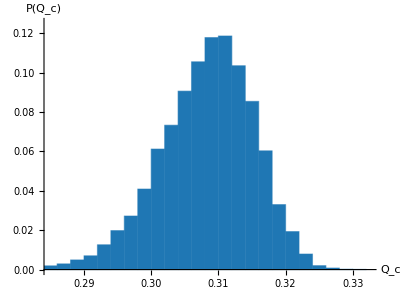

```mathematica
fig2bInset=Show[
Histogram[tab1,{0.002},"Probability",PlotRange->{{0.285,0.3325},{0,0.125}},ChartStyle->Directive[blue],PlotRangeClipping->True],
AxesStyle->Directive[Black,Thick,FontSize->20,FontFamily->"Cambria"],AxesLabel->{"Q_c","P(Q_c)"},
AspectRatio->3/4,ImageSize->{Automatic,200}]
```

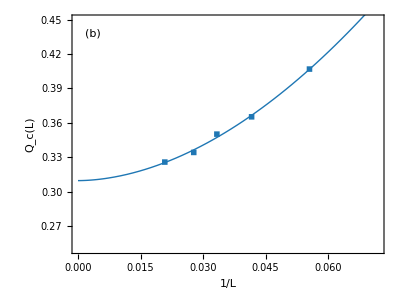
-Graphics-
-Graphics-

```mathematica
fig2b=Show[
ListPlot[qcross,PlotMarkers->{square[blue],0.036},PlotRange->{{0,0.072},{0.25,0.45}}],
Plot[qfit[x],{x,0,0.072},PlotStyle->Directive[blue,Thick]],
Graphics[{FontSize->30,FontFamily->"Cambria",
Text["(b)",{0.05*0.072,0.45-1/16*0.2}],
Inset[fig2bInset,{0.036,0.25},{Left,Bottom}]
}],
Frame->True,FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],FrameLabel->{"1/L","Q_c(L)"},AspectRatio->3/4,ImagePadding->{{95,15},{85,15}},ImageSize->{Automatic,500}]
```

```mathematica
qdlist=ReadList[dir<>"Rv.txt",Number];
qdlist=Partition[qdlist,{4}];
lenlistFull=Sort[Union[Range[18,60,6],{16,20,32,40,64,72,80,96}]];
qdlist1Full=Table[Select[qdlist,Abs[#[[1]]-lenlistFull[[i]]]≤0.0001&],{i,Length[lenlistFull]}];
qdfineFull=Select[Select[#,(0.2499≤#[[2]]≤0.3501(*&&Abs[#[[2]]-0.315]≥0.0001*))&]&/@qdlist1Full,Length[#]≥5&];
qdfitFull=LinearModelFit[#[[;;,{2,3}]],{1,x,x^2},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@qdfineFull;
```

```mathematica
qcval=qfit["ParameterTableEntries"][[1,1]];
slope=Table[{qdfineFull[[i,1,1]],(#[[2,1]]+2*#[[3,1]]*qcval)&@(qdfitFull[[i]]["ParameterTableEntries"])},{i,Length[qdfitFull]}];
yfit=NonlinearModelFit[slope[[;;,{1,2}]],a*l^y,{a,y},l];
yfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0374079 | 0.00316178 | 11.8313 | 2.38796×10^-6
y | 0.809194 | 0.0205552 | 39.3668 | 1.906×10^-10

```mathematica
(*Resampling procedure to estimate the statistical fluctuations*)
qdlist=ReadList[dir<>"Rv.txt",Number];
qdlist=Partition[qdlist,{4}];
lenlistFull=Sort[Union[Range[18,60,6],{16,20,32,40,64,72,80,96}]];
qdlist1Full=Table[Select[qdlist,Abs[#[[1]]-lenlistFull[[i]]]≤0.0001&],{i,Length[lenlistFull]}];
qdfineFull=Select[Select[#,(0.2499≤#[[2]]≤0.3501(*&&Abs[#[[2]]-0.315]≥0.0001*))&]&/@qdlist1Full,Length[#]≥5&];
lenlistSel=qdfineFull[[;;,1,1]];
ilist={1,2,3,4,6};
jlist={4,6,8,9,10};
tab=Table[
shift=Table[RandomVariate[NormalDistribution[],Length[qdfineFull[[i]]]],{i,Length[qdfineFull]}];
sample=qdfineFull;
sample[[;;,;;,3]]=qdfineFull[[;;,;;,3]]+qdfineFull[[;;,;;,4]]*shift;
qdfitSample=LinearModelFit[#[[;;,{2,3}]],{1,x(*,x^2*)},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@sample;
qcrossSample=Table[{1/lenlistSel[[ilist[[i]]]],Select[Solve[qdfitSample[[ilist[[i]]]][x]==qdfitSample[[jlist[[i]]]][x],x][[;;,1,2]],#∈Reals(*&&0.3≤#≤0.8*)&][[1]]},{i,Length[ilist]}];
qfitSample=NonlinearModelFit[qcrossSample,qc+a*x^ω,{{qc,0.3},a,{ω,1.8}},x];
qcvalSample=qfitSample["ParameterTableEntries"][[1,1]];
qdfitFullSample=LinearModelFit[#[[;;,{2,3}]],{1,x,x^2},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@sample;slopeSample=Table[{qdfineFull[[i,1,1]],(#[[2,1]]+2*#[[3,1]]*qcvalSample)&@(qdfitFullSample[[i]]["ParameterTableEntries"])},{i,Length[qdfitFullSample]}];
yfitSample=NonlinearModelFit[slopeSample[[;;,{1,2}]],a*l^y,{a,{y,0.8}},l];
yfitSample["ParameterTableEntries"][[2,1]]
,{i,10000}];
s=OpenWrite[dir<>"ysSamples.txt"];
Write[s,tab];
Close[s];
```

```mathematica
tab=ReadList[dir<>"ysSamples.txt"][[1]];
val=yfit["ParameterTableEntries"][[2,1]]
sd=StandardDeviation[tab]
(*Composition of fitting uncertainty and statistical fluctuations*)
error=Sqrt[yfit["ParameterTableEntries"][[2,2]]^2+sd^2]
```

0.809194

0.0338075

0.039566

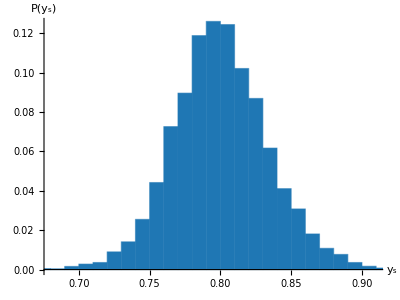

```mathematica
fig2cInset=Show[
Histogram[tab,{0.01},"Probability",PlotRange->{{0.68,0.91},{0,0.125}},ChartStyle->Directive[blue],PlotRangeClipping->True],
AxesStyle->Directive[Black,Thick,FontSize->20,FontFamily->"Cambria"],AxesLabel->{"y_s","P(y_s)"},
AspectRatio->3/4,ImageSize->{Automatic,200}]
```

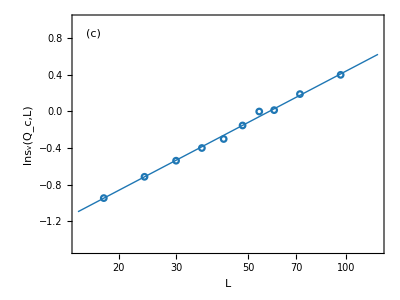
-Graphics-
-Graphics-

```mathematica
logslope={#[[1]],Log[Abs[#[[2]]]]}&/@slope;
fig2c=Show[
ListLogLinearPlot[logslope,PlotMarkers->{circle[blue],0.036},PlotRange->{{15,125},{-1.5,1}}],LogLogPlot[yfit[x],{x,15,125},PlotStyle->Directive[blue,Thick]],
Graphics[{FontSize->30,FontFamily->"Cambria",
Text["(c)",{Log[15]+0.05*Log[125/15],1-1/16*2.5}],
Inset[fig2cInset,{Log[15*125]/2,-1.5},{Left,Bottom}]
}],
Axes->None,Frame->True,FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],FrameLabel->{"L","lns_v(Q_c,L)"},AspectRatio->3/4,ImagePadding->{{100,5},{85,15}},ImageSize->{Automatic,500}]
```

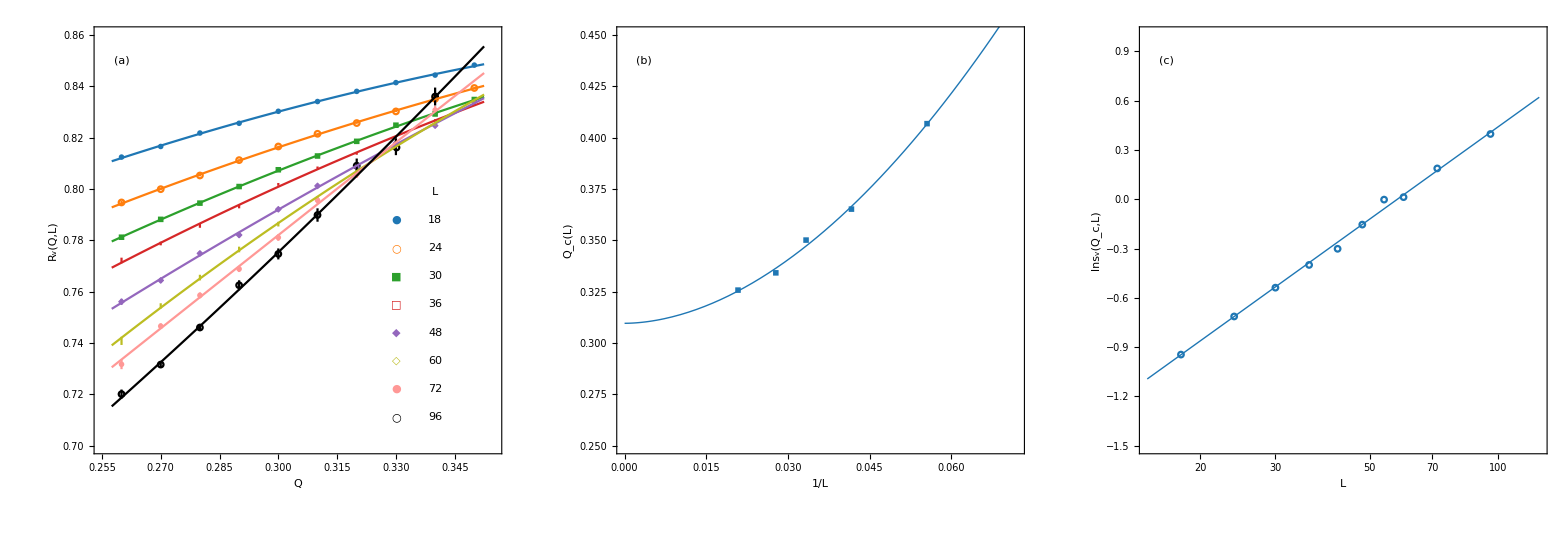

```mathematica
fig2=GraphicsRow[{fig2a,fig2b,fig2c},Spacings->0]
Export[figdir<>"binder.pdf",fig2,"PDF"];
```

### Fig. 3: Scaling dimensions

```mathematica
cplist=ReadList[dir<>"Cp.txt",Number];
cplist=Partition[cplist,{4}];
cplist1=Select[cplist,Abs[#[[2]]-0.31]≤0.0001&][[2;;]];
cpfit1=NonlinearModelFit[cplist1[[;;,{1,3}]],a*x^-(2*Δ),{a,Δ},x,Weights->1/cplist1[[;;,4]]^2,VarianceEstimatorFunction->(1&)];
cpfit1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.78725 | 0.0172998 | 103.31 | 8.60784×10^-14
Δ | 0.664298 | 0.00148098 | 448.554 | 6.83345×10^-19

```mathematica
(*Resampling procedure to estimate the statistical fluctuations*)
cplenlist=Union@cplist[[;;,1]];
cplistlen=Select[Table[Select[cplist,#[[1]]==cplenlist[[i]]&&#[[1]]≥18&&0.2599<#[[2]]<0.3501&&Abs[#[[2]]-0.315]>0.0001&],{i,Length[cplenlist]}],Length[#]≥9&];
cplenlist=Union@@cplistlen[[;;,;;,1]];
cpInterpol=LinearModelFit[#[[;;,{2,3}]],{1,x,x^2,x^3(*,x^4*)},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@cplistlen;
qdlist=ReadList[dir<>"Rv.txt",Number];
qdlist=Partition[qdlist,{4}];
lenlist={18,24,30,36,48,60,72,96};
qdlist1=Table[Select[qdlist,Abs[#[[1]]-lenlist[[i]]]≤0.0001&],{i,Length[lenlist]}];
qdfine=Select[#,(0.2599≤#[[2]]≤0.3501&&Abs[#[[2]]-0.315]≥0.0001)&]&/@qdlist1;
DsSamples=Table[
shift=Table[RandomVariate[NormalDistribution[],Length[qdfine[[i]]]],{i,Length[qdfine]}];
sample=qdfine;
sample[[;;,;;,3]]=qdfine[[;;,;;,3]]+qdfine[[;;,;;,4]]*shift;
qdfitSample=LinearModelFit[#[[;;,{2,3}]],{1,x(*,x^2*)},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@sample;
qcrossSample=Table[{1/lenlist[[i]],Select[Solve[qdfitSample[[i]][x]==qdfitSample[[i+3]][x],x][[;;,1,2]],#∈Reals(*&&0.3≤#≤0.8*)&][[1]]},{i,1,5}];
qfitSample=NonlinearModelFit[qcrossSample,qc+a*x^ω,{qc,a,ω},x];
qcvalSample=qfitSample["ParameterTableEntries"][[1,1]];
cpSample=Table[{cplenlist[[i]],cpInterpol[[i]][qcvalSample]},{i,Length[cplenlist]}];
cpfitSample=NonlinearModelFit[cpSample,a*x^-(2*Δ),{a,Δ},x];
cpfitSample["ParameterTableEntries"][[2,1]]
,{i,10000}];
s=OpenWrite[dir<>"DsSamples.txt"];
Write[s,DsSamples];
Close[s];
```

```mathematica
DsSamples=ReadList[dir<>"DsSamples.txt"][[1]];
val=cpfit1["ParameterTableEntries"][[2,1]]
sd=StandardDeviation[DsSamples]
(*Composition of fitting uncertainty and statistical fluctuations*)
DsError=Sqrt[cpfit1["ParameterTableEntries"][[2,2]]^2+sd^2]
```

0.664298

0.0160381

0.0161064

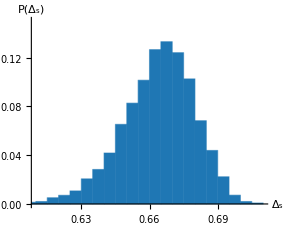

```mathematica
fig3aInset=Show[
Histogram[DsSamples,{0.005},"Probability",PlotRange->{{0.61,0.71},{0,0.15}},ChartStyle->Directive[blue],PlotRangeClipping->True],
AxesStyle->Directive[Black,Thick,FontSize->20,FontFamily->"Cambria"],AxesLabel->{"Δ_s","P(Δ_s)"},
AspectRatio->4/5,ImageSize->{285,225}]
```

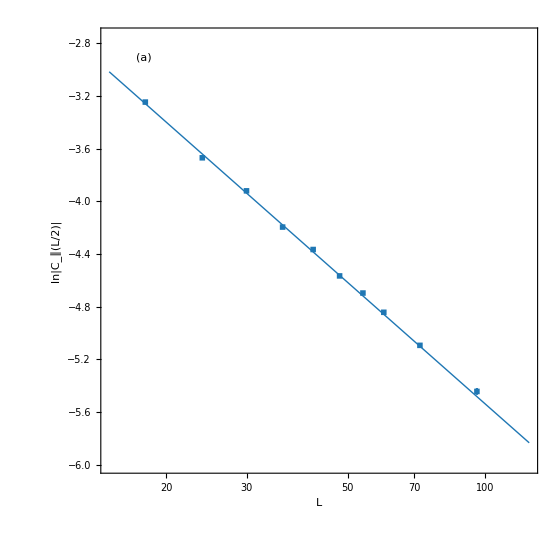
-Graphics-
-Graphics-

```mathematica
fig3a=Show[
LogLinearPlot[Log@cpfit1[x],{x,15,125},PlotStyle->Directive[blue,Thick],PlotRange->{{15,125},{-6,-2.75}}],
ErrorListPlot[formErrList[{Log[#[[1]]],Log[#[[2]]],#[[3]]/#[[2]]}&/@(cplist1[[;;,{1,3,4}]])],PlotStyle->blue,PlotMarkers->{square[blue],0.032}],
Graphics[{
Black,FontSize->30,FontFamily->"Cambria",
Text["(a)",{Log[15]+1/12*Log[125/15],-2.75-0.05*3.25}],
Inset[fig3aInset,{Log[15.6],-6},{Left,Bottom}]
}],
Axes->None,Frame->True,FrameLabel->{"L","ln|C_∥(L/2)|"},FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],ImageSize->{560,540},ImagePadding->{{105,5},{80,10}},AspectRatio->1]
```

```mathematica
mslist=ReadList[dir<>"Sm.txt",Number];
mslist=Partition[mslist,{4}];
mslist[[;;,{3,4}]]*=mslist[[;;,1]];
mslist1=Select[mslist,Abs[#[[2]]-0.31]≤0.0001&][[2;;]];
msfit1=NonlinearModelFit[mslist1[[;;,{1,3}]],c+a*x^-(2*Δ-1),{{c,5},{a,3},{Δ,0.65}},x,Weights->1/mslist1[[;;,4]]^2,VarianceEstimatorFunction->(1&)];
msfit1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
c | 3.90958 | 0.135563 | 28.8396 | 1.55068×10^-8
a | -2.77217 | 0.0564502 | -49.1083 | 3.79995×10^-10
Δ | 0.620979 | 0.0135383 | 45.8685 | 6.11911×10^-10

```mathematica
(*Resampling procedure to estimate the statistical fluctuations*)
mslenlist=Union@mslist[[;;,1]];
mslistlen=Select[Table[Select[mslist,#[[1]]==mslenlist[[i]]&&#[[1]]≥18&&0.2599<#[[2]]<0.3501&&Abs[#[[2]]-0.315]>0.0001&],{i,Length[mslenlist]}],Length[#]≥9&];
mslenlist=Union@@mslistlen[[;;,;;,1]];
msInterpol=LinearModelFit[#[[;;,{2,3}]],{1,x,x^2,x^3(*,x^4*)},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@mslistlen;
qdlist=ReadList[dir<>"Rv.txt",Number];
qdlist=Partition[qdlist,{4}];
lenlist={18,24,30,36,48,60,72,96};
qdlist1=Table[Select[qdlist,Abs[#[[1]]-lenlist[[i]]]≤0.0001&],{i,Length[lenlist]}];
qdfine=Select[#,(0.2599≤#[[2]]≤0.3501&&Abs[#[[2]]-0.315]≥0.0001)&]&/@qdlist1;
DsSamples2=Table[
shift=Table[RandomVariate[NormalDistribution[],Length[qdfine[[i]]]],{i,Length[qdfine]}];
sample=qdfine;
sample[[;;,;;,3]]=qdfine[[;;,;;,3]]+qdfine[[;;,;;,4]]*shift;
qdfitSample=LinearModelFit[#[[;;,{2,3}]],{1,x(*,x^2*)},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@sample;
qcrossSample=Table[{1/lenlist[[i]],Select[Solve[qdfitSample[[i]][x]==qdfitSample[[i+3]][x],x][[;;,1,2]],#∈Reals(*&&0.3≤#≤0.8*)&][[1]]},{i,1,5}];
qfitSample=NonlinearModelFit[qcrossSample,qc+a*x^ω,{qc,a,ω},x];
qcvalSample=qfitSample["ParameterTableEntries"][[1,1]];
msSample=Table[{mslenlist[[i]],msInterpol[[i]][qcvalSample]},{i,Length[mslenlist]}];
msfitSample=NonlinearModelFit[msSample,c+a*x^-(2*Δ-1),{{c,4},{a,-2.7},{Δ,0.6}},x,MaxIterations->1000]//Quiet;
msfitSample["ParameterTableEntries"][[3,1]]
,{i,10000}];
s=OpenWrite[dir<>"DsSamples2.txt"];
Write[s,DsSamples2];
Close[s];
```

```mathematica
DsSamples2=ReadList[dir<>"DsSamples2.txt"][[1]];
val=msfit1["ParameterTableEntries"][[3,1]]
sd=StandardDeviation[DsSamples2]
(*Composition of fitting uncertainty and statistical fluctuations*)
DsError2=Sqrt[msfit1["ParameterTableEntries"][[3,2]]^2+sd^2]
```

0.620979

0.0443116

0.0463336

```mathematica
(*Composition of the values of Subscript[Δ, s] estimated from C_∥ and Subscript[m, s]^2*)
val=(cpfit1["ParameterTableEntries"][[2,1]]/DsError^2+msfit1["ParameterTableEntries"][[3,1]]/DsError2^2)/(1/DsError^2+1/DsError2^2)
err=1/Sqrt[1/DsError^2+1/DsError2^2]
```

0.659628

0.0152134

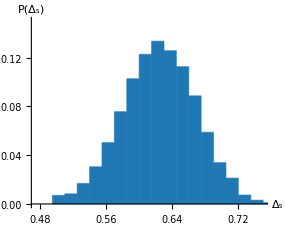

```mathematica
fig3bInset=Show[
Histogram[DsSamples2,{0.015},"Probability",PlotRange->{{0.475,0.75},{0,0.15}},ChartStyle->Directive[blue],PlotRangeClipping->True],
AxesStyle->Directive[Black,Thick,FontSize->20,FontFamily->"Cambria"],AxesLabel->{"Δ_s","P(Δ_s)"},
AspectRatio->4/5,ImageSize->{285,225}]
```

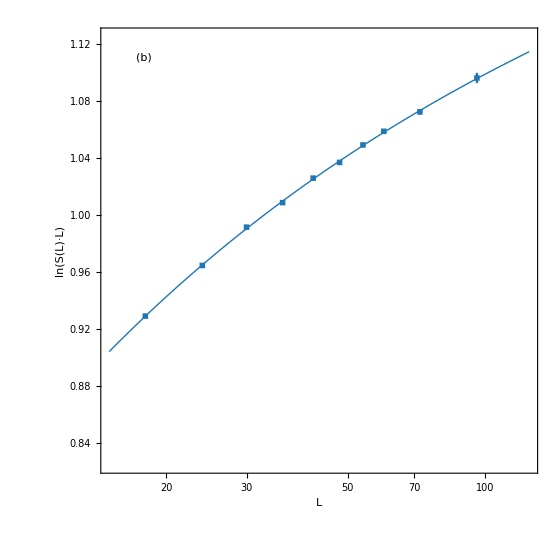
-Graphics-
-Graphics-

```mathematica
fig3b=Show[
LogLinearPlot[Log@msfit1[x],{x,15,125},PlotStyle->Directive[blue,Thick],PlotRange->{{15,125},{0.825,1.125}}],
ErrorListPlot[formErrList[{Log[#[[1]]],Log[#[[2]]],#[[3]]/#[[2]]}&/@(mslist1[[;;,{1,3,4}]])],PlotStyle->blue,PlotMarkers->{square[blue],0.032}],
Graphics[{
Black,FontSize->30,FontFamily->"Cambria",
Text["(b)",{Log[15]+1/12*Log[125/15],1.125-0.05*0.3}],
Inset[fig3bInset,{Log[120],0.825},{Right,Bottom}]
}],
Axes->None,Frame->True,FrameLabel->{"L","ln(S(L)·L)"},FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],ImageSize->{560,540},ImagePadding->{{105,5},{80,10}},AspectRatio->1]
```

```mathematica
md2list=ReadList[dir<>"Mv2.txt",Number];
md2list=Partition[md2list,{4}];
md2list[[;;,{3,4}]]*=md2list[[;;,1]];
md2list1=Select[md2list,Abs[#[[2]]-0.31]≤0.0001&][[2;;]];
md2fit1=NonlinearModelFit[md2list1[[;;,{1,3}]],c+a*x^-(2*Δ-1),{a,{Δ,0.2},c},x,Weights->1/md2list1[[;;,4]]^2,VarianceEstimatorFunction->(1&)];
md2fit1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.294526 | 0.0129271 | 22.7837 | 7.94895×10^-8
Δ | 0.213043 | 0.00428141 | 49.76 | 3.46577×10^-10
c | -0.196593 | 0.0300181 | -6.54915 | 0.000319082

```mathematica
(*Resampling procedure to estimate the statistical fluctuations*)
md2lenlist=Union@md2list[[;;,1]];
md2listlen=Select[Table[Select[md2list,#[[1]]==md2lenlist[[i]]&&#[[1]]≥18&&0.2599<#[[2]]<0.3501&&Abs[#[[2]]-0.315]>0.0001&],{i,Length[md2lenlist]}],Length[#]≥9&];
md2lenlist=Union@@md2listlen[[;;,;;,1]];
md2Interpol=LinearModelFit[#[[;;,{2,3}]],{1,x,x^2,x^3(*,x^4*)},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@md2listlen;
qdlist=ReadList[dir<>"Rv.txt",Number];
qdlist=Partition[qdlist,{4}];
lenlist={18,24,30,36,48,60,72,96};
qdlist1=Table[Select[qdlist,Abs[#[[1]]-lenlist[[i]]]≤0.0001&],{i,Length[lenlist]}];
qdfine=Select[#,(0.2599≤#[[2]]≤0.3501&&Abs[#[[2]]-0.315]≥0.0001)&]&/@qdlist1;
DvSamples=Table[
shift=Table[RandomVariate[NormalDistribution[],Length[qdfine[[i]]]],{i,Length[qdfine]}];
sample=qdfine;
sample[[;;,;;,3]]=qdfine[[;;,;;,3]]+qdfine[[;;,;;,4]]*shift;
qdfitSample=LinearModelFit[#[[;;,{2,3}]],{1,x(*,x^2*)},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@sample;
qcrossSample=Table[{1/lenlist[[i]],Select[Solve[qdfitSample[[i]][x]==qdfitSample[[i+3]][x],x][[;;,1,2]],#∈Reals(*&&0.3≤#≤0.8*)&][[1]]},{i,1,5}];
qfitSample=NonlinearModelFit[qcrossSample,qc+a*x^ω,{qc,a,ω},x];
qcvalSample=qfitSample["ParameterTableEntries"][[1,1]];
md2Sample=Table[{md2lenlist[[i]],md2Interpol[[i]][qcvalSample]},{i,Length[md2lenlist]}];
md2fitSample=NonlinearModelFit[md2Sample,c+a*x^-(2*Δ-1),{a,{Δ,0.2},c},x,MaxIterations->1000]//Quiet;
md2fitSample["ParameterTableEntries"][[2,1]]
,{i,10000}];
s=OpenWrite[dir<>"DvSamples.txt"];
Write[s,DvSamples];
Close[s];
```

```mathematica
DvSamples=ReadList[dir<>"DvSamples.txt"][[1]];
val=md2fit1["ParameterTableEntries"][[2,1]]
sd=StandardDeviation[DvSamples]
(*Composition of fitting uncertainty and statistical fluctuations*)
DvError=Sqrt[md2fit1["ParameterTableEntries"][[3,2]]^2+sd^2]
```

0.213043

0.034353

0.0456204

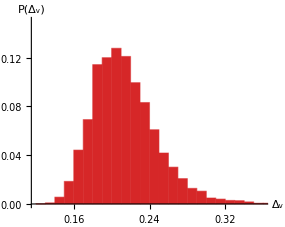

```mathematica
fig3cInset=Show[
Histogram[DvSamples,{0.01},"Probability",PlotRange->{{0.12,0.36},{0,0.15}},ChartStyle->Directive[red],PlotRangeClipping->True],
AxesStyle->Directive[Black,Thick,FontSize->20,FontFamily->"Cambria"],AxesLabel->{"Δ_v","P(Δ_v)"},
AspectRatio->4/5,ImageSize->{285,225}]
```

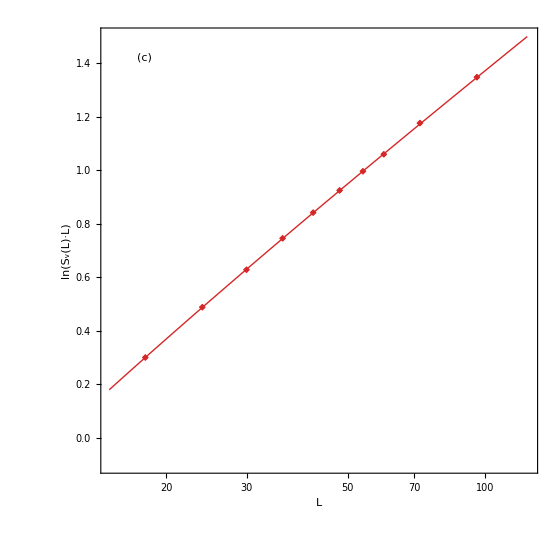
-Graphics-
-Graphics-

```mathematica
fig3c=Show[
LogLinearPlot[Log@md2fit1[x],{x,15,125},PlotStyle->Directive[red,Thick],PlotRange->{{15,125},{-0.1,1.5}}],
ErrorListPlot[formErrList[{Log[#[[1]]],Log[#[[2]]],#[[3]]/#[[2]]}&/@(md2list1[[;;,{1,3,4}]])],PlotStyle->red,PlotMarkers->{diam[red],0.032}],
Graphics[{
Black,FontSize->30,FontFamily->"Cambria",
Text["(c)",{Log[15]+1/12*Log[125/15],1.5-0.05*1.6}],
Inset[fig3cInset,{Log[120],-0.1},{Right,Bottom}]
}],
Axes->None,Frame->True,FrameLabel->{"L","ln(S_v(L)·L)"},FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],ImageSize->{560,540},ImagePadding->{{105,5},{80,10}},AspectRatio->1]
```

```mathematica
mdlist=ReadList[dir<>"Mv.txt",Number];
mdlist=Partition[mdlist,{4}];
mdlist1=Select[mdlist,Abs[#[[2]]-0.31]≤0.0001&][[2;;]];
mdfit1=NonlinearModelFit[mdlist1[[;;,{1,3}]],a*x^-Δ,{a,Δ},x,Weights->1/mdlist1[[;;,4]]^2,VarianceEstimatorFunction->(1&)];
mdfit1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.449709 | 0.00102047 | 440.689 | 7.87226×10^-19
Δ | 0.202862 | 0.000697701 | 290.757 | 2.19193×10^-17

```mathematica
(*Resampling procedure to estimate the statistical fluctuations*)
mdlenlist=Union@mdlist[[;;,1]];
mdlistlen=Select[Table[Select[mdlist,#[[1]]==mdlenlist[[i]]&&#[[1]]≥18&&0.2599<#[[2]]<0.3501&&Abs[#[[2]]-0.315]>0.0001&],{i,Length[mdlenlist]}],Length[#]≥9&];
mdlenlist=Union@@mdlistlen[[;;,;;,1]];
mdInterpol=LinearModelFit[#[[;;,{2,3}]],{1,x,x^2,x^3(*,x^4*)},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@mdlistlen;
qdlist=ReadList[dir<>"Rv.txt",Number];
qdlist=Partition[qdlist,{4}];
lenlist={18,24,30,36,48,60,72,96};
qdlist1=Table[Select[qdlist,Abs[#[[1]]-lenlist[[i]]]≤0.0001&],{i,Length[lenlist]}];
qdfine=Select[#,(0.2599≤#[[2]]≤0.3501&&Abs[#[[2]]-0.315]≥0.0001)&]&/@qdlist1;
DvSamples2=Table[
shift=Table[RandomVariate[NormalDistribution[],Length[qdfine[[i]]]],{i,Length[qdfine]}];
sample=qdfine;
sample[[;;,;;,3]]=qdfine[[;;,;;,3]]+qdfine[[;;,;;,4]]*shift;
qdfitSample=LinearModelFit[#[[;;,{2,3}]],{1,x(*,x^2*)},x,Weights->1/#[[;;,4]]^2,VarianceEstimatorFunction->(1&)]&/@sample;
qcrossSample=Table[{1/lenlist[[i]],Select[Solve[qdfitSample[[i]][x]==qdfitSample[[i+3]][x],x][[;;,1,2]],#∈Reals(*&&0.3≤#≤0.8*)&][[1]]},{i,1,5}];
qfitSample=NonlinearModelFit[qcrossSample,qc+a*x^ω,{qc,a,ω},x];
qcvalSample=qfitSample["ParameterTableEntries"][[1,1]];
mdSample=Table[{mdlenlist[[i]],mdInterpol[[i]][qcvalSample]},{i,Length[mdlenlist]}];
mdfitSample=NonlinearModelFit[mdSample,a*x^-Δ,{a,Δ},x,MaxIterations->1000];
mdfitSample["ParameterTableEntries"][[2,1]]
,{i,10000}];
s=OpenWrite[dir<>"DvSamples2.txt"];
Write[s,DvSamples2];
Close[s];
```

```mathematica
DvSamples2=ReadList[dir<>"DvSamples2.txt"][[1]];
val=mdfit1["ParameterTableEntries"][[2,1]]
sd=StandardDeviation[DvSamples2]
(*Composition of fitting uncertainty and statistical fluctuations*)
DvError2=Sqrt[mdfit1["ParameterTableEntries"][[2,2]]^2+sd^2]
```

0.202862

0.0148992

0.0149155

```mathematica
(*Composition of Subscript[Δ, v] values estimated from v^2 and |v|*)
val=(md2fit1["ParameterTableEntries"][[2,1]]/DvError^2+mdfit1["ParameterTableEntries"][[2,1]]/DvError2^2)/(1/DvError^2+1/DvError2^2)
err=1/Sqrt[1/DvError^2+1/DvError2^2]
```

0.203845

0.014177

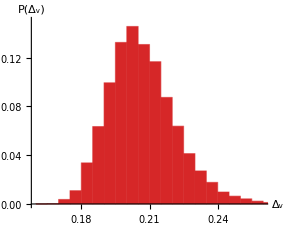

```mathematica
fig3dInset=Show[
Histogram[DvSamples2,{0.005},"Probability",PlotRange->{{0.16,0.26},{0,0.15}},ChartStyle->Directive[red],PlotRangeClipping->True],
AxesStyle->Directive[Black,Thick,FontSize->20,FontFamily->"Cambria"],AxesLabel->{"Δ_v","P(Δ_v)"},
AspectRatio->4/5,ImageSize->{285,225}]
```

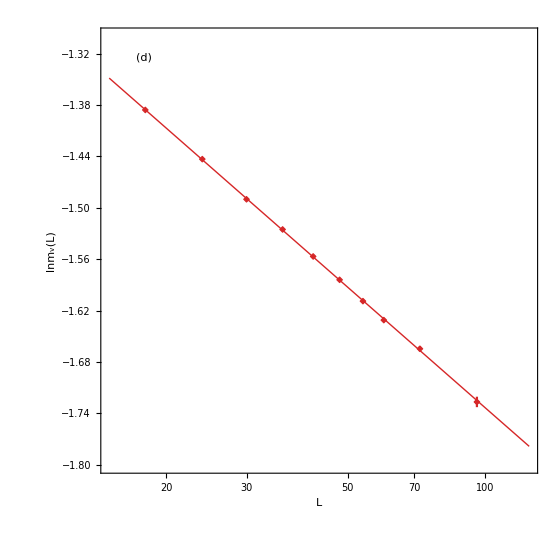
-Graphics-
-Graphics-

```mathematica
fig3d=Show[
LogLinearPlot[Log@mdfit1[x],{x,15,125},PlotStyle->Directive[red,Thick],PlotRange->{{15,125},{-1.8,-1.3}}],
ErrorListPlot[formErrList[{Log[#[[1]]],Log[#[[2]]],#[[3]]/#[[2]]}&/@(mdlist1[[;;,{1,3,4}]])],PlotStyle->red,PlotMarkers->{diam[red],0.032}],
Graphics[{
Black,FontSize->30,FontFamily->"Cambria",
Text["(d)",{Log[15]+1/12*Log[125/15],-1.3-0.05*0.5}],
Inset[fig3dInset,{Log[15.6],-1.8},{Left,Bottom}]
}],
Axes->None,Frame->True,FrameLabel->{"L","lnm_v(L)"},FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],ImageSize->{560,540},ImagePadding->{{105,5},{80,10}},AspectRatio->1]
```

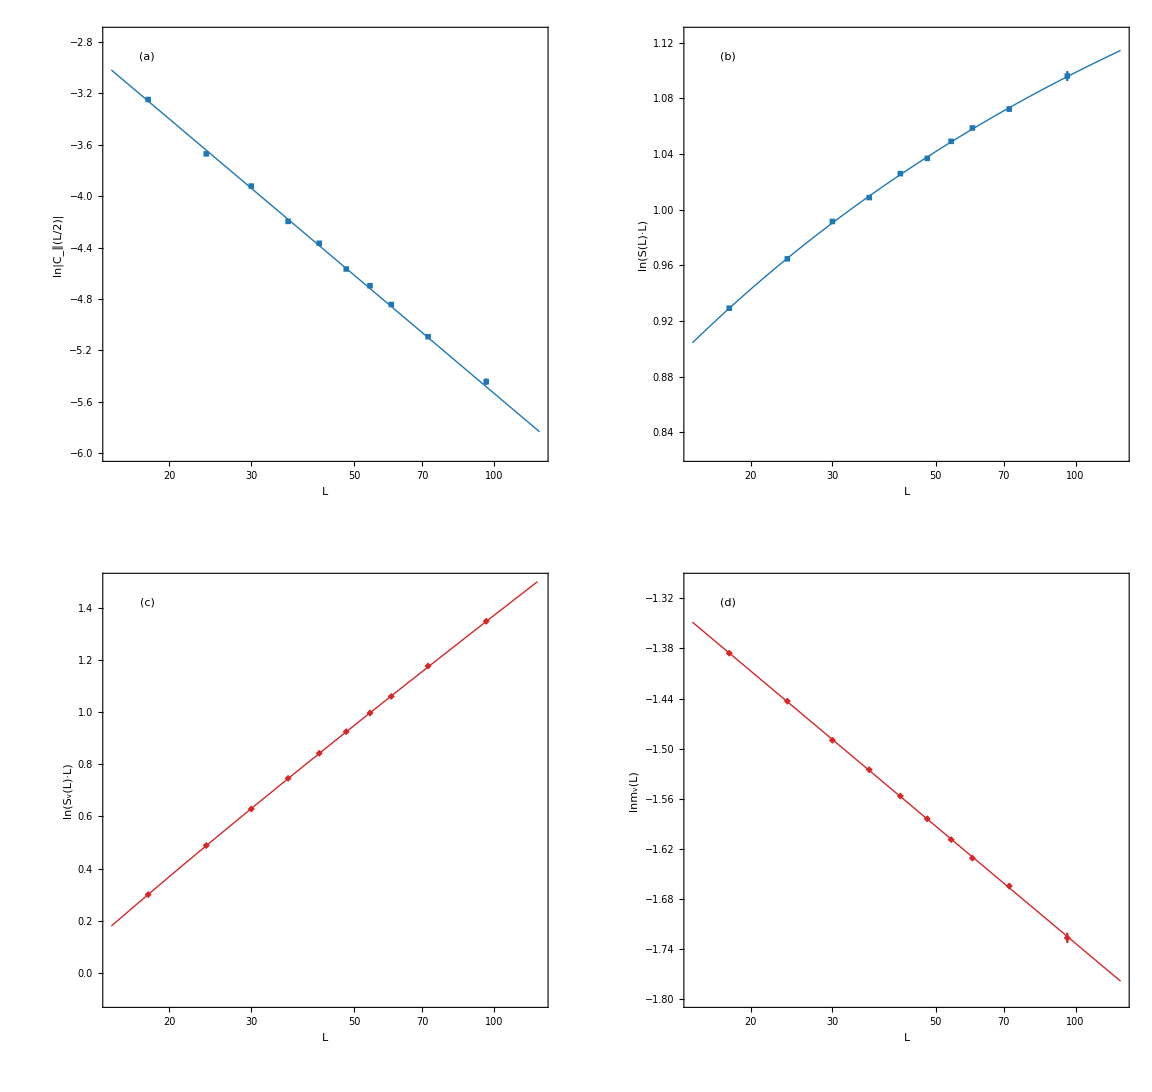

```mathematica
fig3=GraphicsGrid[{{fig3a,fig3b},{fig3c,fig3d}},Spacings->{10,0}]
Export[figdir<>"cor.pdf",fig3,"PDF"];
```

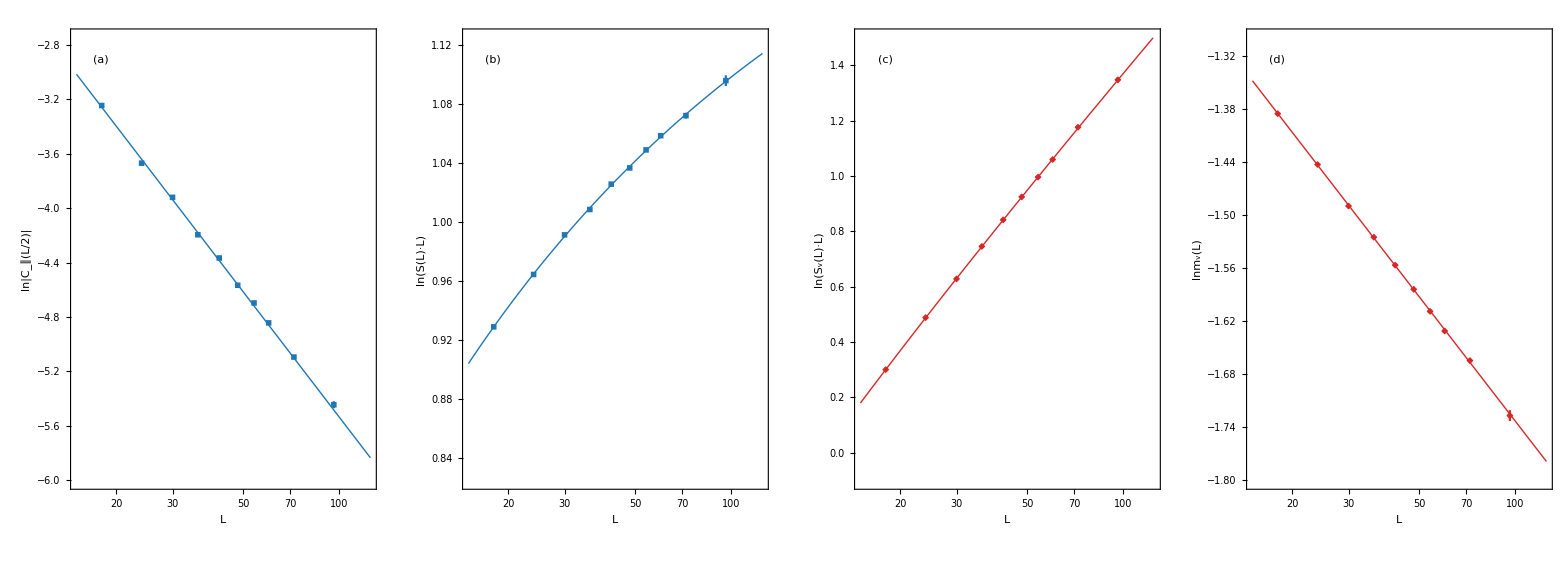

```mathematica
fig3s=GraphicsRow[{fig3a,fig3b,fig3c,fig3d},Spacings->0]
Export[figdir<>"cors.pdf",fig3s,"PDF"];
```

### Fig. 4: Order parameters

```mathematica
lm=1;
cplist=ReadList[dir<>"Cp.txt",Number];
cplist=Partition[cplist,{4}];
q3select={0,0.12,0.24,0.28,0.32(*,0.4*)};
cplist=Table[Select[cplist,Abs[#[[2]]-q3select[[i]]]≤0.0001&],{i,Length[q3select]}];
cplist[[;;,;;,1]]=1/cplist[[;;,;;,1]];
fcp=Table[LinearModelFit[cplist[[i,lm;;,{1,3}]],{1,x,x^2,x^3},x,Weights->1/cplist[[i,lm;;,4]]^2],{i,Length[q3select]}];
```

```mathematica
lm=1;
mslist=ReadList[dir<>"Sm.txt",Number];
mslist=Partition[mslist,{4}];
q3=Sort@Union@mslist[[;;,2]];
q3select={0,0.12,0.24,0.28,0.32(*,0.4*)};
mslist=Table[Select[mslist,Abs[#[[2]]-q3select[[i]]]≤0.0001&],{i,Length[q3select]}];
mslist[[;;,;;,1]]=1/mslist[[;;,;;,1]];
fms=Table[LinearModelFit[mslist[[i,lm;;,{1,3}]],{1,x,-x*Log[x],x^2},x,Weights->1/mslist[[i,lm;;,4]]^2],{i,Length[q3select]}];
```

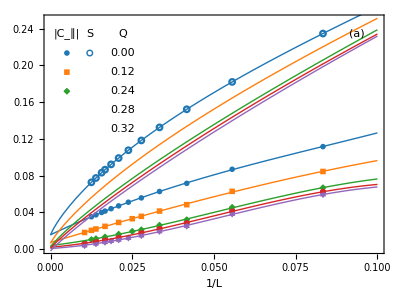
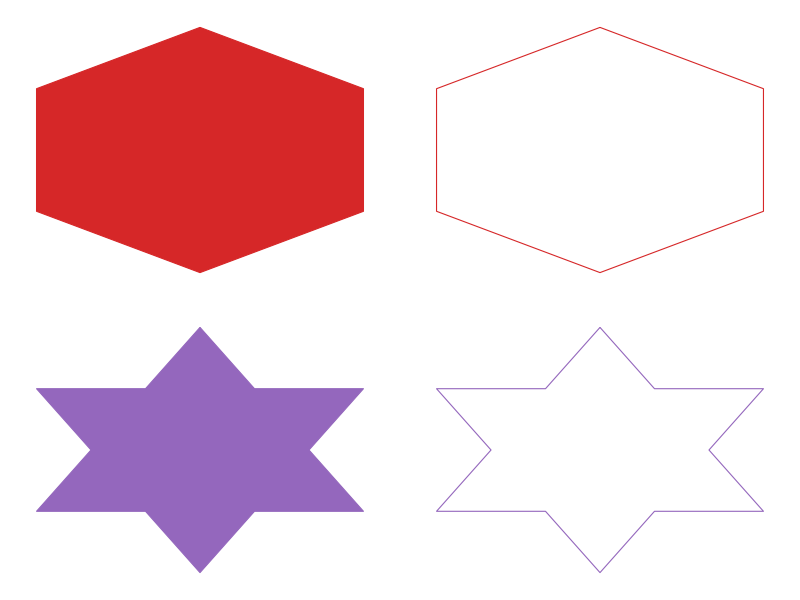

```mathematica
markers={disk,square,diam,hex,star6};
markers2={circle,rect,diame,hexe,star6e};
colors={blue,orange,green,red,purple};
fig4a=Show[
ErrorListPlot[formErrList/@(cplist[[;;,;;,{1,3,4}]]),PlotMarkers->Table[{markers[[i]][colors[[i]]],0.032},{i,Length[markers]}],PlotStyle->colors,PlotRange->{{0,0.1},{0,0.25}}],
Table[Plot[fcp[[i]][x],{x,0,0.1},PlotStyle->Directive[colors[[i]],Thick]],{i,Length[colors]}],
ErrorListPlot[formErrList/@(mslist[[;;,;;,{1,3,4}]]),PlotMarkers->Table[{markers2[[i]][colors[[i]]],0.032},{i,Length[markers2]}],PlotStyle->colors,PlotRange->{{0,0.1},{0,0.25}}],
Table[Plot[fms[[i]][x],{x,0,0.1},PlotStyle->Directive[colors[[i]],Thick]],{i,Length[colors]}],
Graphics[{FontSize->30,FontFamily->"Cambria",
Text["(a)",{0.1-1/16*0.1,0.25-1/16*0.25},Background->White],
Text["|C_∥|",{0.005,0.25*(1-1/16)}],
Text["S",{0.012,0.25*(1-1/16)}],
Text["Q",{0.022,0.25*(1-1/16)}],
Table[Inset[markers[[i]][colors[[i]]],{0.005,0.25*(1-(i+3/4)/12)},{Center,Center},0.0024],{i,Length[colors]}],
Table[Inset[markers2[[i]][colors[[i]]],{0.012,0.25*(1-(i+3/4)/12)},{Center,Center},0.0024],{i,Length[colors]}],
Table[{Text[myToString[q3select[[i]],2],{0.022,0.25*(1-(i+3/4)/12)}]},{i,Length[colors]}]
}],
Frame->True,FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],FrameLabel->{"1/L",""},AspectRatio->3/4,ImagePadding->{{60,30},{80,10}},ImageSize->{Automatic,500}]
```

```mathematica
lm=1;
mdsqlist=ReadList[dir<>"Mv2.txt",Number];
mdsqlist=Partition[mdsqlist,{4}];
q3=Sort@Union@mdsqlist[[;;,2]];
q3select={0.24,0.26,0.28,0.30,0.32,0.34};
mdsqlist=Table[Select[mdsqlist,Abs[#[[2]]-q3select[[i]]]≤0.0001&],{i,Length[q3select]}];
mdsqlist[[;;,;;,1]]=1/mdsqlist[[;;,;;,1]];
fmdsq=Table[LinearModelFit[mdsqlist[[i,lm;;,{1,3}]],{1,x,-x*Log[x],x^2},x,Weights->1/mdsqlist[[i,lm;;,4]]^2,VarianceEstimatorFunction->(1&)],{i,Length[q3select]}];
```

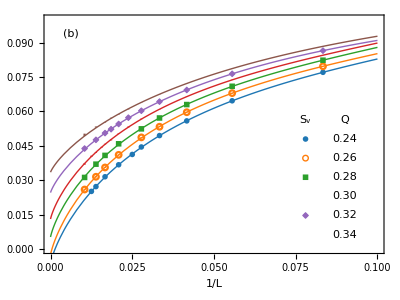

```mathematica
markers={disk,circle,square,rect,diam,diame};
colors={blue,orange,green,red,purple,brown};
fig4b=Show[
ErrorListPlot[formErrList/@(mdsqlist[[;;,;;,{1,3,4}]]),PlotMarkers->Table[{markers[[i]][colors[[i]]],0.032},{i,Length[markers]}],PlotStyle->colors,PlotRange->{{0,0.1},{0,0.1}}],
Table[Plot[fmdsq[[i]][x],{x,0,0.1},PlotStyle->Directive[colors[[i]],Thick]],{i,Length[fmdsq]}],
Graphics[{FontSize->30,FontFamily->"Cambria",
Text["(b)",{1/16*0.1,0.1-1/16*0.1}],
Text["S_v",{0.078,0.1*(6+3/4)/12}],
Text["Q",{0.09,0.1*(6+3/4)/12}],
Table[Inset[markers[[i]][colors[[i]]],{0.078,0.1*(6+3/4-i)/12},{Center,Center},0.0024],{i,Length[q3select]}],Table[{Text[myToString[q3select[[i]],2],{0.09,0.1*(6+3/4-i)/12}]},{i,Length[q3select]}]
}],
Frame->True,FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],FrameLabel->{"1/L",""},AspectRatio->3/4,ImagePadding->{{60,30},{80,10}},ImageSize->{Automatic,500}]
```

```mathematica
lm=1;
cplist=ReadList[dir<>"Cp.txt",Number];
cplist=Partition[cplist,{4}];
q3=Select[Sort@Union[cplist[[;;,2]]],#≤0.32&];
cplist=Select[Table[Select[cplist,Abs[#[[2]]-q3[[i]]]≤0.0001&],{i,Length[q3]}],Length[#]≥5&];
cplist[[;;,;;,1]]=1/cplist[[;;,;;,1]];
q3=Sort@Union[Flatten@cplist[[;;,;;,2]]];
fcp=Table[LinearModelFit[cplist[[i,lm;;,{1,3}]],{1,x,x^2,x^3},x,Weights->1/cplist[[i,lm;;,4]]^2,VarianceEstimatorFunction->(1&)],{i,Length[q3]}];
af2=Table[{q3[[i]],fcp[[i]]["ParameterTableEntries"][[1,1]],fcp[[i]]["ParameterTableEntries"][[1,2]]}
,{i,Length[q3]}];
af2=Select[af2,#[[2]]≥0&];
```

```mathematica
lm=1;
mslist=ReadList[dir<>"Sm.txt",Number];
mslist=Partition[mslist,{4}];
q3=Select[Sort@Union[mslist[[;;,2]]],#≤0.32&];
mslist=Select[Table[Select[mslist,Abs[#[[2]]-q3[[i]]]≤0.0001&],{i,Length[q3]}],Length[#]≥5&];
mslist[[;;,;;,1]]=1/mslist[[;;,;;,1]];
q3=Sort@Union[Flatten@mslist[[;;,;;,2]]];
fms=Table[LinearModelFit[mslist[[i,lm;;,{1,3}]],{1,x,-x*Log[x],x^2(*,x^3*)},x,Weights->1/mslist[[i,lm;;,4]]^2,VarianceEstimatorFunction->(1&)],{i,Length[q3]}];
af=Table[{q3[[i]],fms[[i]]["ParameterTableEntries"][[1,1]],fms[[i]]["ParameterTableEntries"][[1,2]]}
,{i,Length[q3]}];
af=Select[af,#[[2]]≥0&];
```

```mathematica
lm=1;
mdlist=ReadList[dir<>"Mv2.txt",Number];
mdlist=Partition[mdlist,{4}];
q3=Select[Sort@Union[mdlist[[;;,2]]],1≥#≥0.26&];
mdlist=Select[Table[Select[mdlist,Abs[#[[2]]-q3[[i]]]≤0.0001&],{i,Length[q3]}],Length[#]≥5&];
mdlist[[;;,;;,1]]=1/mdlist[[;;,;;,1]];
q3=Sort@Union[Flatten@mdlist[[;;,;;,2]]];
fmd=Table[LinearModelFit[mdlist[[i,lm;;,{1,3}]],{1,x,-x*Log[x],x^2},x,Weights->1/mdlist[[i,lm;;,4]]^2,VarianceEstimatorFunction->(1&)],{i,Length[q3]}];
vbs=Table[{q3[[i]],fmd[[i]]["ParameterTableEntries"][[1,1]],fmd[[i]]["ParameterTableEntries"][[1,2]]}
,{i,Length[q3]}];
vbs=Select[vbs,#[[2]]≥0&];
```

```mathematica
fig4c=Show[
ErrorListPlot[formErrList@af,PlotMarkers->{circle[blue],0.032},PlotStyle->blue,PlotRange->{{0,1},{0,0.1}},PlotRangeClipping->False],
ErrorListPlot[formErrList@af2,PlotMarkers->{rect[green],0.032},PlotStyle->green,PlotRange->{{0,1},{0,0.1}}],
ErrorListPlot[formErrList@vbs,PlotMarkers->{diam[red],0.032},PlotStyle->red,PlotRange->{{0,1.025},{0,0.1}}],
Graphics[{
blue,BSplineCurve[af[[;;,{1,2}]],SplineWeights->1/Abs[af[[;;,3]]]^2],
green,BSplineCurve[af2[[;;,{1,2}]],SplineWeights->1/Abs[af2[[;;,3]]]^2],
red,BSplineCurve[vbs[[;;,{1,2}]],SplineWeights->1/Abs[vbs[[;;,3]]]^2]
}],
Graphics[{FontSize->30,FontFamily->"Cambria",
Text["(c)",{1/16*1.0,0.1-1/16*0.1}],
Text["m_s^2 by |C_∥|",{0.75,0.1*2.5/8},{-1,0}],
Text["m_s^2 by S",{0.75,0.1*1.5/8},{-1,0}],
Text["m_v^2 by S_v",{0.75,0.1*0.5/8},{-1,0}],
Inset[circle[blue],{0.7,0.1*2.5/8},{Center,Center},0.024],
Inset[rect[green],{0.7,0.1*1.5/8},{Center,Center},0.024],
Inset[diam[red],{0.7,0.1*0.5/8},{Center,Center},0.024]
}],
Frame->True,FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],FrameLabel->{"Q",""},AspectRatio->3/4,ImagePadding->{{60,20},{80,10}},ImageSize->{Automatic,500}]
```

-Graphics-

```mathematica
fig4=GraphicsRow[{fig4a,fig4b,fig4c},Spacings->0]
Export[figdir<>"order.pdf",fig4,"PDF"];
```

-Graphics-

### Fig. 5: Ordinary correlation

```mathematica
cplist=ReadList[dir<>"Cp.txt",Number];
cplist=Partition[cplist,{4}];
q3=Select[Sort@Union[cplist[[;;,2]]],#≥0.3&];
cplist=Select[Table[Select[cplist,Abs[#[[2]]-q3[[i]]]≤0.0001&&#[[1]]≥18&&#[[1]]≠20&],{i,Length[q3]}],Length[#]≥5&];
q3=Sort@Union[Flatten@cplist[[;;,;;,2]]];
```

```mathematica
q3sel={0.3,0.32,0.36,0.4,0.5,0.6,0.9,1.2};
cpsel=Table[Select[cplist,Abs[#[[1,2]]-q3sel[[i]]]≤0.0001&][[1]],{i,Length[q3sel]}];
cpselfit=Table[NonlinearModelFit[cpsel[[i,2;;,{1,3}]],a*x^-(2*Δ),{a,{Δ,0.5}},x,Weights->1/cpsel[[i,2;;,4]]^2,VarianceEstimatorFunction->(1&)],{i,Length[q3sel]}];
```

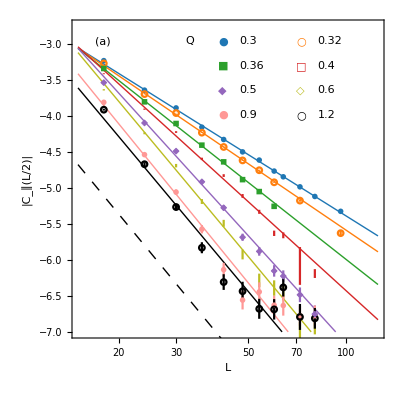

```mathematica
markers={disk,circle,square,rect,diam,diame,disk,circle};
markerstxt={"●","○","■","□","◆","◇","●","○"};
colors={blue,orange,green,red,purple,yellow,pink,Black};
fig5a=Show[
Table[LogLinearPlot[Log@cpselfit[[i]][x],{x,15,125},PlotStyle->Directive[colors[[i]],Thick],PlotRange->{{15,125},{-7,-2.75}}],{i,Length[cpsel]}],
ErrorListPlot[Table[formErrList[{Log[#[[1]]],Log[#[[2]]],#[[3]]/#[[2]]}&/@(cpsel[[i,;;,{1,3,4}]])],{i,Length[cpsel]}],PlotMarkers->Table[{markers[[i]][colors[[i]]],0.024},{i,Length[markers]}],PlotStyle->colors],
LogLogPlot[6*len^-(2*1.194),{len,15,125},PlotStyle->Directive[Black,Thick,Dashing[0.02]]],
Graphics[{FontSize->30,FontFamily->"Cambria",
Text["(a)",{Log[15]+1/12*Log[125/15],-2.75-0.05*4.25}],
Text["Q",{3.5,-2.75-0.05*4.25}],
Table[{{colors[[i]],FontSize->20,Text[markerstxt[[i]],{3.7+(i-1)*0.55,-2.75-0.05*4.25},{-1,0}]},
Text[q3sel[[i]],{3.85+(i-1)*0.55,-2.75-0.05*4.25},{-1,0}]},{i,2}],
Table[{{colors[[i]],FontSize->20,Text[markerstxt[[i]],{3.7+(i-3)*0.55,-2.75-0.13*4.25},{-1,0}]},
Text[q3sel[[i]],{3.85+(i-3)*0.55,-2.75-0.13*4.25},{-1,0}]},{i,3,4}],
Table[{{colors[[i]],FontSize->20,Text[markerstxt[[i]],{3.7+(i-5)*0.55,-2.75-0.21*4.25},{-1,0}]},
Text[q3sel[[i]],{3.85+(i-5)*0.55,-2.75-0.21*4.25},{-1,0}]},{i,5,6}],
Table[{{colors[[i]],FontSize->20,Text[markerstxt[[i]],{3.7+(i-7)*0.55,-2.75-0.29*4.25},{-1,0}]},
Text[q3sel[[i]],{3.85+(i-7)*0.55,-2.75-0.29*4.25},{-1,0}]},{i,7,8}]
}],
Frame->True,FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],FrameLabel->{"L","|C_∥(L/2)|"},AspectRatio->1,ImagePadding->{{80,5},{80,15}},ImageSize->{Automatic,500}]
```

```mathematica
cpfit=Table[NonlinearModelFit[cplist[[i,2;;,{1,3}]],a*x^-(2*Δ),{a,{Δ,0.5}},x,Weights->1/cplist[[i,2;;,4]]^2,MaxIterations->1000,VarianceEstimatorFunction->(1&)],{i,Length[q3]}];
cpdims=Table[Flatten@{q3[[i]],cpfit[[i]]["ParameterTableEntries"][[2,1;;2]]},{i,Length[cplist]}];
```

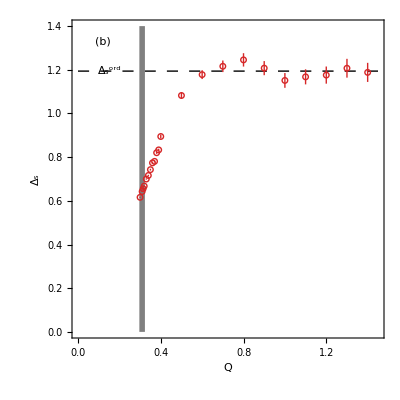

```mathematica
fig5b=Show[
Plot[1.194,{x,0,1.45},PlotStyle->Directive[Dashing[0.02],Thick,Black],PlotRange->{{0,1.45},{0,1.4}}],
Graphics[{
{Gray,Thickness[0.01],Line[{{0.310,0},{0.310,1.4}}]},
FontSize->30,FontFamily->"Cambria",
Text["Δ_s^ord",{0.155,1.194},{0,0},Background->White],
Text["(b)",{1/12*1.45,1.4-0.05*1.4}]
}],
ErrorListPlot[formErrList@cpdims,PlotMarkers->{circle[red],0.024},PlotStyle->Directive[Thick,red],PlotRange->{{-0.025,1.45},{0,1.4}}],Frame->True,FrameStyle->Directive[Black,Thick,FontSize->30,FontFamily->"Cambria"],FrameLabel->{"Q","Δ_s"},AspectRatio->1,ImagePadding->{{80,20},{80,15}},ImageSize->{Automatic,500}]
```

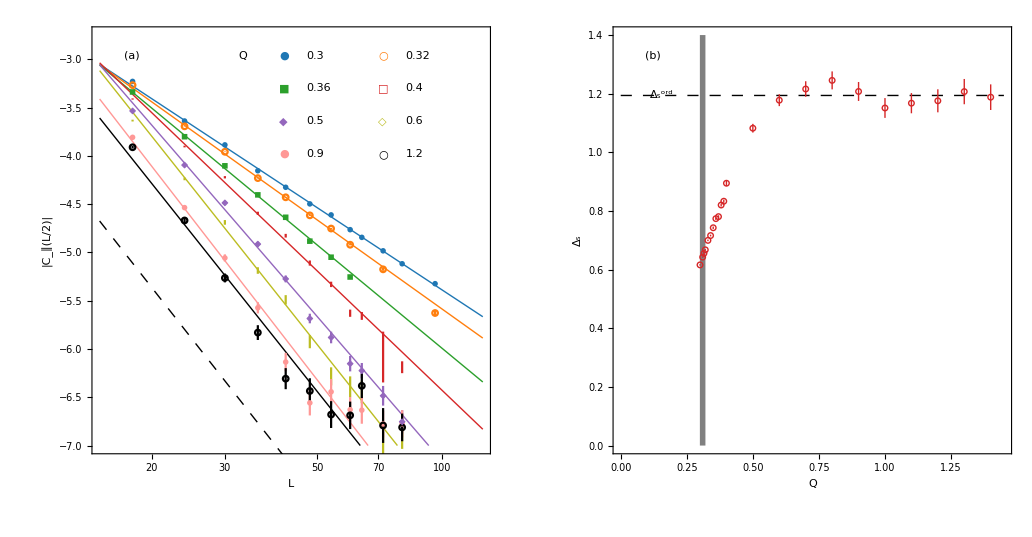

```mathematica
fig5=GraphicsRow[{fig5a,fig5b},Spacings->10]
Export[figdir<>"ord.pdf",fig5,"PDF"];
```

### Appendix: Extraordinary-log trial fitting

```mathematica
cplist=ReadList[dir<>"Cp.txt",Number];
cplist=Partition[cplist,{4}];
mslist=ReadList[dir<>"Sm.txt",Number];
mslist=Partition[mslist,{4}];
```

```mathematica
cp00=Select[cplist,Abs[#[[2]]-0]≤0.0001&];
cpex=Table[NonlinearModelFit[cp00[[lm;;,{1,3}]],a*(Log[L]+c)^-q,{a,{q,1},{c,0.1}},L,Weights->1/cp00[[lm;;,4]]^2,VarianceEstimatorFunction->(1&),MaxIterations->100000(*,PrecisionGoal->15*)],{lm,Length[cp00]-5}];
Prepend[Table[Flatten@{cp00[[lm,1]],cpex[[lm]]["ParameterTableEntries"][[1;;3,1;;2]],chi2dof[cp00[[lm;;,{1,3,4}]],cpex[[lm]],Length[cp00[[lm;;]]]-3]},{lm,Length[cp00]-5}],{"L_min","a","a_err","q_(||)","q_(||,err)","c","c_err","χ^2/d.o.f."}]//Grid
```

L_min | a | a_err | q_(||) | q_(||,err) | c | c_err | χ^2/d.o.f.
12 | 1.2073×10^7 | 8.6221×10^6 | 7.59169 | 0.202898 | 8.94421 | 0.331809 | 35.2055
18 | 2707.77 | 1243.78 | 5.086 | 0.146863 | 4.76107 | 0.242093 | 13.8922
24 | 338291. | 468810. | 6.55519 | 0.407546 | 7.24888 | 0.685256 | 10.961
30 | 562.077 | 515.298 | 4.58442 | 0.300748 | 3.8841 | 0.50837 | 6.67098
36 | 8.19258×10^6 | 3.81289×10^7 | 7.4613 | 1.3104 | 8.85223 | 2.25263 | 3.86907
42 | 329.328 | 710.289 | 4.41433 | 0.711911 | 3.56274 | 1.22704 | 2.11807
48 | 276840. | 2.37955×10^6 | 6.48692 | 2.5092 | 7.1889 | 4.37383 | 2.023

```mathematica
ms00=Select[mslist,Abs[#[[2]]-0]≤0.0001&];
msex=Table[NonlinearModelFit[ms00[[lm;;,{1,3}]],a*(Log[L]+c)^-q,{a,{q,1},{c,0}},L,Weights->1/ms00[[lm;;,4]]^2,VarianceEstimatorFunction->(1&),MaxIterations->10^3,PrecisionGoal->10],{lm,Length[ms00]-5}];
Prepend[Table[Flatten@{ms00[[lm,1]],msex[[lm]]["ParameterTableEntries"][[1;;3,1;;2]],chi2dof[ms00[[lm;;,{1,3,4}]],msex[[lm]],Length[ms00[[lm;;]]]-3]},{lm,Length[ms00]-5}],{"L_min","a","a_err","q_(||)","q_(||,err)","c","c_err","χ^2/d.o.f."}]//Grid
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of NonlinearModelFit :: cvmit will be suppressed during this calculation.

L_min | a | a_err | q_(||) | q_(||,err) | c | c_err | χ^2/d.o.f.
12 | 7.11054×10^8 | 2.42007×10^8 | 8.5485 | 0.093883 | 10.3552 | 0.151523 | 482.321
18 | 1.77248×10^7 | 7.47269×10^6 | 7.53609 | 0.120375 | 8.58136 | 0.194922 | 251.064
24 | 767090. | 395766. | 6.64353 | 0.152687 | 7.02101 | 0.247952 | 122.643
30 | 118542. | 76968.7 | 6.09745 | 0.196997 | 6.05898 | 0.320813 | 68.4876
36 | 21034.3 | 17304.4 | 5.57749 | 0.256278 | 5.14877 | 0.418763 | 45.7002
42 | 3331.65 | 3377.19 | 5.00602 | 0.326546 | 4.1509 | 0.534806 | 24.0027
48 | 890.322 | 1200.53 | 4.58391 | 0.446595 | 3.41365 | 0.733812 | 16.8433

```mathematica
ms00=Select[mslist,Abs[#[[2]]-0]≤0.0001&];
msex=Table[NonlinearModelFit[ms00[[lm;;,{1,3}]],a*(Log[L]+c)^-q,{a,{q,1},{c,0}},L,Weights->1/ms00[[lm;;,4]]^2,VarianceEstimatorFunction->(1&),MaxIterations->10^4,PrecisionGoal->10],{lm,Length[ms00]-5}];
Prepend[Table[Flatten@{ms00[[lm,1]],msex[[lm]]["ParameterTableEntries"][[1;;3,1;;2]],chi2dof[ms00[[lm;;,{1,3,4}]],msex[[lm]],Length[ms00[[lm;;]]]-3]},{lm,Length[ms00]-5}],{"L_min","a","a_err","q_(||)","q_(||,err)","c","c_err","χ^2/d.o.f."}]//Grid
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

General::stop: Further output of NonlinearModelFit :: cvmit will be suppressed during this calculation.

L_min | a | a_err | q_(||) | q_(||,err) | c | c_err | χ^2/d.o.f.
12 | 6.25931×10^30 | 3.19111×10^-19 | 20.7711 | 0.000989577 | 30.0919 | 0.00566282 | 20.6226
18 | 5.23789×10^25 | 5.32024×10^-19 | 18.1538 | 0.00114013 | 25.7813 | 0.00628688 | 11.0483
24 | 1.23758×10^21 | 1.59165×10^-18 | 15.6926 | 0.00133189 | 21.7209 | 0.00704338 | 3.55652
30 | 1.232×10^18 | 6.73302×10^-19 | 14.0463 | 0.00155001 | 19.0072 | 0.00793618 | 1.93405
36 | 1.24399×10^16 | 5.4049×10^-18 | 12.926 | 0.00190928 | 17.1589 | 0.00954762 | 2.252
42 | 1.63438×10^13 | 2.41317×10^-16 | 11.2666 | 0.00228636 | 14.4061 | 0.0109388 | 0.802602
48 | 4.79312×10^11 | 1.03143×10^-14 | 10.358 | 0.00284612 | 12.9024 | 0.0132624 | 1.11823

```mathematica
ms00=Select[mslist,Abs[#[[2]]-0]≤0.0001&];
msex=Table[NonlinearModelFit[ms00[[lm;;,{1,3}]],a*(Log[L]+c)^-q,{a,{q,1},{c,0}},L,Weights->1/ms00[[lm;;,4]]^2,VarianceEstimatorFunction->(1&),MaxIterations->10^5,PrecisionGoal->10],{lm,Length[ms00]-5}];
Prepend[Table[Flatten@{ms00[[lm,1]],msex[[lm]]["ParameterTableEntries"][[1;;3,1;;2]],chi2dof[ms00[[lm;;,{1,3,4}]],msex[[lm]],Length[ms00[[lm;;]]]-3]},{lm,Length[ms00]-5}],{"L_min","a","a_err","q_(||)","q_(||,err)","c","c_err","χ^2/d.o.f."}]//Grid
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

L_min | a | a_err | q_(||) | q_(||,err) | c | c_err | χ^2/d.o.f.
12 | 3.24911×10^51 | 2.41934×10^-18 | 30.8671 | 0.00135584 | 46.4037 | 0.0086105 | 4.20044
18 | 3.82617×10^41 | 1.30201×10^-18 | 26.1377 | 0.0015185 | 38.7203 | 0.00925829 | 3.21406
24 | 3.41896×10^29 | 4.14631×10^-18 | 20.1417 | 0.0016162 | 28.9507 | 0.00919573 | 1.19761
30 | 2.30776×10^24 | 1.41312×10^-18 | 17.4503 | 0.00183089 | 24.5536 | 0.0100167 | 0.785788
36 | 8.83797×10^24 | 1.13646×10^-18 | 17.7581 | 0.00243417 | 25.0579 | 0.0134296 | 0.937942
42 | 2.08427×10^17 | 7.60077×10^-19 | 13.6221 | 0.00263734 | 18.2651 | 0.013436 | 0.45483
48 | 3.67671×10^18 | 3.7269×10^-18 | 14.3161 | 0.00362813 | 19.4079 | 0.0188361 | 0.591442

## Useful subroutines

```mathematica
blue=RGBColor["#1f77b4"];
orange=RGBColor["#ff7f0e"];
green=RGBColor["#2ca02c"];
red=RGBColor["#d62728"];
purple=RGBColor["#9467bd"];
yellow=RGBColor["#bcbd22"];
pink=RGBColor["#ff9896"];
brown=RGBColor["#8c564b"];
disk[color_]:=Graphics[{color,Disk[]}];
circle[color_]:=Graphics[{color,Thick,Circle[]}];
square[color_]:=Graphics[{color,Rectangle[{-1,-1},{1,1}]}];
rect[color_]:=Graphics[{EdgeForm[{color,Thick}],FaceForm[Transparent],Rectangle[{-1,-1},{1,1}]}];
diam[color_]:=Graphics[{EdgeForm[{color,Thick}],FaceForm[color],Polygon[{{1,0},{0,1},{-1,0},{0,-1}}]}];
diame[color_]:=Graphics[{EdgeForm[{color,Thick}],FaceForm[Transparent],Polygon[{{1,0},{0,1},{-1,0},{0,-1}}]}];
hex[color_]:=Graphics[{EdgeForm[{color,Thick}],FaceForm[color],Polygon[Table[{Sin[2*Pi/6*i],Cos[2*Pi/6*i]},{i,0,5}]]}];
hexe[color_]:=Graphics[{EdgeForm[{color,Thick}],FaceForm[Transparent],Polygon[Table[{Sin[2*Pi/6*i],Cos[2*Pi/6*i]},{i,0,5}]]}];
dots=Flatten[Transpose@{Table[{Cos[2*Pi/6*i+Pi/2],Sin[2*Pi/6*i+Pi/2]},{i,0,5}],1/Sqrt[3]*Table[{Cos[2*Pi/6*i],Sin[2*Pi/6*i]},{i,2,7}]},1];
star6[color_]:=Graphics[{EdgeForm[{color,Thick}],FaceForm[color],Polygon[dots]}];
star6e[color_]:=Graphics[{EdgeForm[{color,Thick}],FaceForm[Transparent],Polygon[dots]}];
cross[color_]:=Graphics[{color,Thick,Line[{{-1,-1},{1,1}}],,Line[{{-1,1},{1,-1}}]}];
plus[color_]:=Graphics[{color,Thick,Line[{{0,-1},{0,1}}],,Line[{{-1,0},{1,0}}]}];
Needs["ErrorBarPlots`"];
formErrList[list_]:={{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@list;
formErrXList[list_]:={{#[[1]],#[[2]]},ErrorBar[#[[3]],0]}&/@list;
formErrYList[list_]:={{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@list;
formErrXYList[list_]:={{#[[1]],#[[2]]},ErrorBar[#[[3]],#[[4]]]}&/@list;
chi2dof[data_,fit_,dof_]:=If[Length[data[[1]]]>3,Total[((fit@@#)&/@(data[[;;,1;;-3]])-data[[;;,-2]])^2/data[[;;,-1]]^2]/dof,Total[(fit/@(data[[;;,1]])-data[[;;,-2]])^2/data[[;;,-1]]^2]/dof];
```

```mathematica
toString[i_Integer]:=If[i<10,"  "<>ToString[i],If[i<100," "<>ToString[i],ToString[i]]];
myToString[x_,digits_]:=ToString[NumberForm[x,{Infinity,digits}]];
label[lmin_,lmax_,di_,digits_]:={#,myToString[#,digits]}&/@Range[lmin,lmax,di];
label[lmin_,lmax_,di_]:={#,""}&/@Range[lmin,lmax,di];
chi2dof[data_,fit_,dof_]:=If[Length[data[[1]]]>3,Total[((fit@@#)&/@(data[[;;,1;;-3]])-data[[;;,-2]])^2/data[[;;,-1]]^2]/dof,Total[(fit/@(data[[;;,1]])-data[[;;,-2]])^2/data[[;;,-1]]^2]/dof];
```